```mathematica
u={3,-2,2};
v={1,-1,-3};
i={1,0,0};
j={0,1,0};
k={0,0,1};

r1={Cos[t],Sin[Sin[Pi/2-t]],t^2};
r2={Exp[t] Cos[t],Exp[t],Exp[t]Sin[t]};
rPrime=D[r2,t];
rDoubPrime=D[r2,{t,2}];

P={1,3,5};
Q={-1,-1,7};
R={0,-2,1};
```

```mathematica
(* Problem 1 *)
(* a *) Norm[u+2v]
(* b *) Cross[Norm[u-v],u] (* DNE *)
(* c *) Projection[v,u]
(* d *) Cross[v,u]
(* e *) Norm[Cross[u,v]]
(* f *) (u.v).(i+j) (* DNE *)
(* g *) VectorAngle[v,u-Projection[u,v]]
```

√57

√30×{3,-2,2}

{-3/17,2/17,-2/17}

{-8,-11,1}

√186

(-1).{1,1,0}

π/2

```mathematica
(*======================================================================================*)
```

```mathematica
(* Problem 2 *)
rTanVec=D[r1,t]

rTan1=rTanVec/.t->0
rTan2=rTanVec/.t->Pi/4

pt1=r1/.t->0
pt2 =r1/.t->Pi/4

Line1={pt1[[1]]+t rTan1[[1]],pt1[[2]]+t rTan1[[2]],pt1[[3]] + t rTan1[[3]]}
Line2={pt2[[1]]+t rTan2[[1]],pt2[[2]]+t rTan2[[2]],pt2[[3]] + t rTan2[[3]]}//FullSimplify
```

{-Sin[t],-Cos[Cos[t]] Sin[t],2 t}

{0,0,0}

{-1/(√2),-Cos[1/(√2)]/(√2),π/2}

{1,Sin[1],0}

{1/(√2),Sin[1/(√2)],π^2/16}

{1,Sin[1],0}

{-(-1+t)/(√2),-(t Cos[1/(√2)])/(√2)+Sin[1/(√2)],1/16 π (π+8 t)}

```mathematica
(*======================================================================================*)
```

```mathematica
(* Problem 3 *)
PQ=Q-P
PR=R-P

normal=Cross[PQ,PR]

Plane={normal[[1]](x-P[[1]])+normal[[2]](y-P[[2]])+normal[[3]](z-P[[3]])==0}

IntCurve=Solve[Plane/.{x->2Cos[t],y->2Sin[t]},z]
zCpt=IntCurve[[1,1,2]];

curve=ParametricPlot3D[{2Cos[t],2Sin[t],zCpt},{t,0,2Pi}]

Show[{
Graphics3D[{
n=20;
xaxis={Arrow[{{-n/4,0,0},{n/2,0,0}}]},
yaxis={Arrow[{{0,-n/4,0},{0,n/2,0}}]},
zaxis={Arrow[{{0,0,-n/4},{0,0,3n/4}}]}
},
	Boxed->False
],
	curve
},
	ImageSize->Scaled[0.75],
	ViewPoint->{2.540561826032737,2.2130727965926864,0.31281688747034037},
	ViewVertical->{0.37077681464041623,0.31816761862052645,0.8725215872323445}
]
```

{-2,-4,2}

{-1,-5,-4}

{26,-10,6}

{26 (-1+x)-10 (-3+y)+6 (-5+z)==0}

{{z→1/3 (13-26 Cos[t]+10 Sin[t])}}

-Graphics3D-

-Graphics3D-

```mathematica
(*======================================================================================*)
```

```mathematica
(* Problem 4 *)
(* a *) FunctionDomain[r2,t] (* All Reals *)
(* b *) bAssoc=<|"vel"->D[r2,t],"speed"->Assuming[Element[t,Reals],FullSimplify[Norm[vel]]],"acc"->D[r2,{t,2}]|>;
Row[{Keys[bAssoc][[1]],"->",Values[bAssoc][[1]],"\n",Keys[bAssoc][[2]],"->",Values[bAssoc][[2]],"\n",Keys[bAssoc][[3]],"->",Values[bAssoc][[3]]}]

(* c *)
TVec=Assuming[Element[t,Reals],FullSimplify[rPrime/Norm[rPrime]]]
TVecPrime=D[TVec,t];

(* d *)
NVec = Assuming[Element[t,Reals],FullSimplify[TVecPrime/Norm[TVecPrime]]]

(* e *)
BVec = FullSimplify[Cross[TVec,NVec]]

(* f *)
κ=Assuming[Element[t,Reals],FullSimplify[ArcCurvature[r2,t]]]

(* g *)
aTan=Assuming[Element[t,Reals],FullSimplify[rPrime.rDoubPrime/Norm[rPrime]]]

(* h *)
aNorm=Assuming[Element[t,Reals],FullSimplify[Norm[Cross[rPrime,rDoubPrime]]/Norm[rPrime]]]

Assuming[Element[t,Reals],FullSimplify[aTan TVec + aNorm NVec]]
%==rDoubPrime
```

True

vel->{ⅇ^t Cos[t]-ⅇ^t Sin[t],ⅇ^t,ⅇ^t Cos[t]+ⅇ^t Sin[t]}
speed->√3 ⅇ^t
acc->{-2 ⅇ^t Sin[t],ⅇ^t,2 ⅇ^t Cos[t]}

{(Cos[t]-Sin[t])/(√3),1/(√3),(Cos[t]+Sin[t])/(√3)}

{-(Cos[t]+Sin[t])/(√2),0,(Cos[t]-Sin[t])/(√2)}

{(Cos[t]-Sin[t])/(√6),-√(2/3),(Cos[t]+Sin[t])/(√6)}

1/3 √2 ⅇ^-t

√3 ⅇ^t

√2 ⅇ^t

{-2 ⅇ^t Sin[t],ⅇ^t,2 ⅇ^t Cos[t]}

True

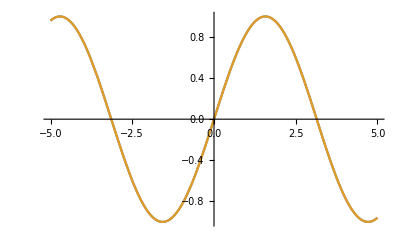

```mathematica
Plot[{Cos[Pi/2-x],Sin[x]},{x,-5,5}]
```